## Defining functions

### Initial testing of calculating H

Test idea for summing rows/columns

```mathematica
Test={{a,b},{c,d},{e,f},{g,h}}
```

{{a,b},{c,d},{e,f},{g,h}}

```mathematica
Test//MatrixForm
```

(a | b
c | d
e | f
g | h)

```mathematica
SumforColumn[x_]:=Sum[Test⟦i,x⟧Test⟦i+1,x⟧,{i,1,Dimensions[Test]⟦1⟧-1}]
```

```mathematica
SumforColumn[1]
```

a c+c e+e g

```mathematica
SumforColumn[2]
```

b d+d f+f h

```mathematica
SumforRow[x_]:=Sum[Test⟦x,i⟧Test⟦x,i+1⟧,{i,1,Dimensions[Test]⟦2⟧-1}]
```

```mathematica
SumforRow[1]
```

a b

```mathematica
SumforRow[2]
```

c d

```mathematica
n=4; (*width *)
m=2;(*length *)
array1=RandomInteger[1,{n,m}]/.{0->-1}
```

{{1,-1},{1,1},{-1,1},{1,-1}}

```mathematica
SumforColumn[x_]:=Sum[array1⟦i,x⟧array1⟦i+1,x⟧,{i,1,Dimensions[array1]⟦1⟧-1}]
```

```mathematica
SumforRow[x_]:=Sum[array1⟦x,i⟧array1⟦x,i+1⟧,{i,1,Dimensions[array1]⟦2⟧-1}]
```

```mathematica
array1//MatrixForm
```

(1 | -1
1 | 1
-1 | 1
1 | -1)

```mathematica
SumforColumn[1]
```

-1

```mathematica
SumforColumn[2]
```

-1

```mathematica
array1[[1,2]]
```

-1

```mathematica
AllColumnSum=Sum[SumforColumn[i],{i,1,Dimensions[array1]⟦2⟧}];
AllRowSum=Sum[SumforRow[i],{i,1,Dimensions[array1]⟦1⟧}];
```

```mathematica
Energy=AllColumnSum+AllRowSum
```

-4

### Time to make a function that takes in an array and calculates H.

```mathematica
energy[array_]:=Sum[Sum[array⟦i,x⟧array⟦i+1,x⟧,{i,1,Dimensions[array]⟦1⟧-1}],{x,1,Dimensions[array]⟦2⟧}]+Sum[Sum[array⟦x,i⟧array⟦x,i+1⟧,{i,1,Dimensions[array]⟦2⟧-1}],{x,1,Dimensions[array1]⟦1⟧}]
```

```mathematica
energy[array1]
```

-4

That checks. Good.

### Now let’s define functions that will determine if something flips

Note kT is being defined as ONE variable.

```mathematica
Prob[DeltaEnergy_,kT_]:=ⅇ^(-DeltaEnergy/kT)
```

Let’s look at the if statements I need.

```mathematica
DeltaEnergy1=-1;
cellvalue=1;
If[DeltaEnergy1≤0,cellvalue/.{1->-1,-1->1},cellvalue]
```

-1

Okay, that flips right. Now we need to deal with the second part of the if statement.

```mathematica
DeltaEnergy1=1;
If[Random[]<Prob[DeltaEnergy1,1],cellvalue/.{1->-1,-1->1},cellvalue]
```

1

Okay, that seems to work (I tried it several times. Sometimes it flips, sometimes it doesn’t. Now let’s try an overall function.

```mathematica
Flip[DeltaEnergy_,cell_,kT_]:=If[DeltaEnergy<0,cell/.{1->-1,-1->1},If[Random[]<Prob[DeltaEnergy,kT],cell/.{1->-1,-1->1},cell]]
```

```mathematica
Flip[1,1,1]
```

-1

Ditto the last comment. This is working. That’s good.

### Now I want to pluck out a single component of an array and apply the flip function to it.

```mathematica
array1
```

{{1,-1},{1,1},{-1,1},{1,-1}}

```mathematica
array1⟦1,1⟧
```

1

```mathematica
array1⟦1,1⟧/.{1->-1,-1->1}
```

-1

```mathematica
array1⟦1,2⟧
```

-1

```mathematica
array1⟦1,2⟧/.{1->-1,-1->1}
```

1

```mathematica
changedarray1=array1/.{array1⟦1,2⟧->array1⟦1,2⟧/.{1->-1,-1->1}}
```

{{1,-1},{1,1},{-1,1},{1,-1}}

That idea failed.

```mathematica
forcedflip[x_]:=x/.{1->-1,-1->1}
```

```mathematica
changedarray2=array1/.{array1⟦1,2⟧->forcedflip[array1⟦1,2⟧]}
```

{{1,1},{1,1},{1,1},{1,1}}

hmm. Well, that was odd. That seems to have changed ALL of the -1’s to 1’s without flipping the others.

```mathematica
forcedflip[-1]
```

1

```mathematica
forcedflip[1]
```

-1

Okay, the problem wasn’t with my simple function.

```mathematica
changedarray3=Block[{a=forcedflip[array1⟦1,2⟧]},array1/.{array1⟦1,2⟧->a}]
```

{{1,1},{1,1},{1,1},{1,1}}

Another failture.

```mathematica
?ReplacePart
```

ReplacePart[expr,i→new] yields an expression in which the i^th part of expr is replaced by new. 
ReplacePart[expr,{i_1→new_1,i_2→new_2,…}] replaces parts at positions i_n by new_n. 
ReplacePart[expr,{i,j,…}→new] replaces the part at position {i,j,…}. 
ReplacePart[expr,{{i_1,j_1,…}→new_1,…}] replaces parts at positions {i_n,j_n,…} by new_n. 
ReplacePart[expr,{{i_1,j_1,…},…}→new] replaces all parts at positions {i_n,j_n,…} by new. 
ReplacePart[i→new] represents an operator form of ReplacePart that can be applied to an expression.

```mathematica
changedarray4=ReplacePart[array1,{1,2}->forcedflip[array1⟦1,2⟧]]
```

{{1,1},{1,1},{-1,1},{1,-1}}

Victory!

Let’s come up with a function

```mathematica
flipcell[i_,j_,array_]:=ReplacePart[array,{i,j}->forcedflip[array⟦i,j⟧]]
```

```mathematica
flipcell[1,2,array1]
```

{{1,1},{1,1},{-1,1},{1,-1}}

```mathematica
flipcell[3,2,array1]
```

{{1,-1},{1,1},{-1,-1},{1,-1}}

Cool, that seems to work.

Now let’s see if the flipping with a certain probability happens

```mathematica
ReplacePart[array1,{1,2}->Flip[-1,array1⟦1,2⟧,1]]
```

{{1,1},{1,1},{-1,1},{1,-1}}

It certainly flips if the change in energy is below 0

```mathematica
ReplacePart[array1,{1,2}->Flip[1,array1⟦1,2⟧,1]]
```

{{1,-1},{1,1},{-1,1},{1,-1}}

And doesn’t flip all the time when I have the change in energy greater than 0. Great. Let’s put this all together into a function that creates a new array if needed after testing a specific component.

```mathematica
ToFlipOrNotToFlip[i_,j_,array_,kT_]:=Block[{deltaEnergy,testarray},
testarray=flipcell[i,j,array];deltaEnergy=energy[testarray]-energy[array];
ReplacePart[array,{i,j}->Flip[deltaEnergy,array⟦i,j⟧,kT]]]
```

```mathematica
array1
```

{{1,-1},{1,1},{-1,1},{1,-1}}

```mathematica
ToFlipOrNotToFlip[1,1,array1,1]
```

{{-1,-1},{1,1},{-1,1},{1,-1}}

This appears to always flip

```mathematica
ToFlipOrNotToFlip[1,2,array1,10]
```

{{1,1},{1,1},{-1,1},{1,-1}}

This appears to flip sometimes--so I made the temperature higher to make sure that it actually flipped.

## Now that I have functions, let’s list them all and then write the code.

- energy[array] takes in an array and computes the hamiltonian
- Prob[DeltaEnergy,kT] takes in a change in energy and a temperature and offers up the probability of a flip happening
-Flip[DeltaEnergy, cell, kT] takes in a change in energy, the value of a single cell, a temperature, and flips the value of that single cell with the probability defined above IF it meets the flip condition.
-ToFlipOrNotToFlip[i,j,array,kT], takes in the indicies of a cell in an array, an array, and the temperature. It outputs a new array, having applied Flip to the index i,j

Now we want to recursively apply ToFlipOrNotToFlip to each component of an array. Once we do that, we want to store that array and then start over. We want to do this for a certain number of time steps. Finally, we want to output an animation.

### Let’s test a single loop. Let’s flip along the columns first

Let’s also use a high temperature to start with so we can see the flips happen.

```mathematica
currentArray=array1
currentArray//MatrixForm
For[i=1,i≤Dimensions[currentArray]⟦1⟧,i++,currentArray=ToFlipOrNotToFlip[i,1,currentArray,20];Print[currentArray//MatrixForm]]
```

{{1,-1},{1,1},{-1,1},{1,-1}}

(1 | -1
1 | 1
-1 | 1
1 | -1)

(-1 | -1
1 | 1
-1 | 1
1 | -1)

(-1 | -1
-1 | 1
-1 | 1
1 | -1)

(-1 | -1
-1 | 1
1 | 1
1 | -1)

(-1 | -1
-1 | 1
1 | 1
-1 | -1)

So the first step flipped (1,1), then the second flip flipped (2,1), the third flipped (3,1), and the last one flipped (4,1). Let’s try with a lower temperature to make sure this doens’t always happen like this

```mathematica
currentArray=array1;
currentArray//MatrixForm
For[i=1,i≤Dimensions[currentArray]⟦1⟧,i++,currentArray=ToFlipOrNotToFlip[i,1,currentArray,1];Print[currentArray//MatrixForm]]
```

(1 | -1
1 | 1
-1 | 1
1 | -1)

(-1 | -1
1 | 1
-1 | 1
1 | -1)

(-1 | -1
1 | 1
-1 | 1
1 | -1)

(-1 | -1
1 | 1
-1 | 1
1 | -1)

«1 more identical outputs»

Okay, good, only one flipped happened that time. Now let’s change this just to output the last array

```mathematica
currentArray=array1;
For[i=1,i≤Dimensions[currentArray]⟦1⟧,i++,currentArray=ToFlipOrNotToFlip[i,1,currentArray,1]]
currentArray
```

{{-1,-1},{1,1},{-1,1},{1,-1}}

### 2nd Loop

Now we want to enclose this in a loop that will deal with our columns. Let’s again make the temperature high so that we can see what’s happening.

```mathematica
Clear[i,j]
```

```mathematica
currentArray=array1;
currentArray//MatrixForm
For[j=1,j≤Dimensions[currentArray]⟦2⟧,j++,For[i=1,i≤Dimensions[currentArray]⟦1⟧,i++,currentArray=ToFlipOrNotToFlip[i,j,currentArray,20];Print[currentArray//MatrixForm]]
currentArray]
```

(1 | -1
1 | 1
-1 | 1
1 | -1)

(-1 | -1
1 | 1
-1 | 1
1 | -1)

(-1 | -1
-1 | 1
-1 | 1
1 | -1)

(-1 | -1
-1 | 1
1 | 1
1 | -1)

(-1 | -1
-1 | 1
1 | 1
-1 | -1)

(-1 | 1
-1 | 1
1 | 1
-1 | -1)

(-1 | 1
-1 | -1
1 | 1
-1 | -1)

(-1 | 1
-1 | -1
1 | -1
-1 | -1)

(-1 | 1
-1 | -1
1 | -1
-1 | 1)

Great! That looks like what we want! Now let’s change it to just output the last array

```mathematica
currentArray=array1;
For[j=1,j≤Dimensions[currentArray]⟦2⟧,j++,For[i=1,i≤Dimensions[currentArray]⟦1⟧,i++,currentArray=ToFlipOrNotToFlip[i,j,currentArray,20];]
currentArray]
currentArray
```

{{-1,1},{-1,-1},{1,-1},{-1,1}}

Now we want to enclose this entirely in a time loop. Let’s remember how append words

### Third loop

```mathematica
?Append
```

Append[expr,elem] gives expr with elem appended. 
Append[elem] represents an operator form of Append that can be applied to an expression.

```mathematica
List1={}
List2=Append[List1,array1]
List3=Append[List2,currentArray]
```

{}

{{{1,-1},{1,1},{-1,1},{1,-1}}}

{{{1,-1},{1,1},{-1,1},{1,-1}},{{-1,1},{-1,-1},{1,-1},{-1,1}}}

That looks easy enough. Now if I want to find just the first set, I want

```mathematica
List3[[1]]
```

{{1,-1},{1,1},{-1,1},{1,-1}}

I can also get the 2nd set

```mathematica
List3[[2]]
```

{{-1,1},{-1,-1},{1,-1},{-1,1}}

```mathematica
tmax=8;
kT=1;
FullData={};
currentArray;
For[t=1,t⩽tmax,t++,
FullData=Append[FullData,currentArray];
For[j=1,j≤Dimensions[currentArray]⟦2⟧,j++,For[i=1,i≤Dimensions[currentArray]⟦1⟧,i++,currentArray=ToFlipOrNotToFlip[i,j,currentArray,kT];]
currentArray]]
FullData
```

{{{-1,1},{1,-1},{-1,1},{1,-1}},{{-1,1},{1,-1},{-1,1},{1,-1}},{{-1,1},{1,-1},{-1,1},{1,-1}},{{-1,1},{1,-1},{-1,1},{1,-1}},{{-1,1},{1,-1},{-1,1},{1,-1}},{{-1,1},{1,-1},{-1,1},{1,-1}},{{-1,1},{1,-1},{-1,1},{1,-1}},{{-1,1},{1,-1},{-1,1},{1,-1}}}

That seems to be working. Now let’s clean it up.

```mathematica
tmax=8; (*Input number of time steps *)
kT=1; (*Input temperature *)
n=4;m=5; (*Input Dimensions *)
FullData={};
currentArray=RandomInteger[1,{n,m}]/.{0->-1}
For[t=1,t⩽tmax,t++,
FullData=Append[FullData,currentArray];
For[j=1,j≤Dimensions[currentArray]⟦2⟧,j++,For[i=1,i≤Dimensions[currentArray]⟦1⟧,i++,currentArray=ToFlipOrNotToFlip[i,j,currentArray,kT];]
currentArray]]
FullData
```

{{-1,-1,-1,1,1},{-1,1,1,-1,1},{-1,1,-1,-1,-1},{1,1,-1,1,-1}}

{{{-1,-1,-1,1,1},{-1,1,1,-1,1},{-1,1,-1,-1,-1},{1,1,-1,1,-1}},{{1,-1,-1,1,-1},{-1,-1,1,-1,1},{-1,1,1,1,-1},{-1,1,-1,1,1}},{{1,1,-1,1,-1},{1,-1,1,-1,1},{-1,-1,-1,1,-1},{1,1,1,-1,1}},{{-1,1,-1,1,-1},{1,-1,1,-1,1},{-1,1,-1,1,-1},{-1,-1,1,-1,1}},{{-1,1,-1,1,-1},{1,-1,1,-1,1},{-1,1,-1,1,-1},{1,-1,1,-1,1}},{{-1,1,-1,1,-1},{1,-1,1,-1,1},{-1,1,-1,1,-1},{1,-1,1,-1,-1}},{{-1,1,-1,1,-1},{1,-1,1,-1,1},{-1,1,-1,1,-1},{1,1,1,-1,1}},{{-1,1,-1,1,-1},{1,-1,1,-1,1},{-1,1,-1,1,-1},{-1,-1,1,-1,1}}}

### Now let’s work on visualization.

```mathematica
FullData⟦1⟧
```

{{-1,-1,-1,1,1},{-1,1,1,-1,1},{-1,1,-1,-1,-1},{1,1,-1,1,-1}}

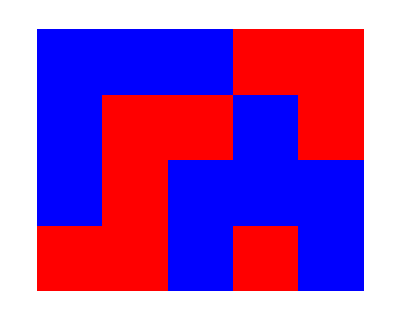

```mathematica
ArrayPlot[FullData⟦1⟧,ColorRules->{1->Red,-1->Blue}]
```

```mathematica
Animate[ArrayPlot[FullData⟦k⟧,ColorRules->{1->Red,-1->Blue}],{k,1,tmax,1}]
```

## Full Code, Take 1

Let’s paste everything together and make it run.

```mathematica
tmax=8; (*Input number of time steps *)
kT=1; (*Input temperature *)
n=4;m=5; (*Input Dimensions *)
FullData={};
currentArray=RandomInteger[1,{n,m}]/.{0->-1}
For[t=1,t⩽tmax,t++,
FullData=Append[FullData,currentArray];
For[j=1,j≤Dimensions[currentArray]⟦2⟧,j++,For[i=1,i≤Dimensions[currentArray]⟦1⟧,i++,currentArray=ToFlipOrNotToFlip[i,j,currentArray,kT];]
currentArray]]
Animate[ArrayPlot[FullData⟦k⟧,ColorRules->{1->Red,-1->Blue}],{k,1,tmax,1}]
```

{{1,-1,1,1,1},{1,1,-1,-1,1},{-1,-1,1,1,-1},{-1,-1,-1,1,1}}

Well, it appears that I have made an ANTI ferromagnetic material. Whoops. Ok, let’s redefine our energy function with a - sign

```mathematica
energy[array_]:=-(Sum[Sum[array⟦i,x⟧array⟦i+1,x⟧,{i,1,Dimensions[array]⟦1⟧-1}],{x,1,Dimensions[array]⟦2⟧}]+Sum[Sum[array⟦x,i⟧array⟦x,i+1⟧,{i,1,Dimensions[array]⟦2⟧-1}],{x,1,Dimensions[array]⟦1⟧}])
```

## Full code, Take 2, wherein I list my function definitions here (now this is the only section that needs to be run)

{}

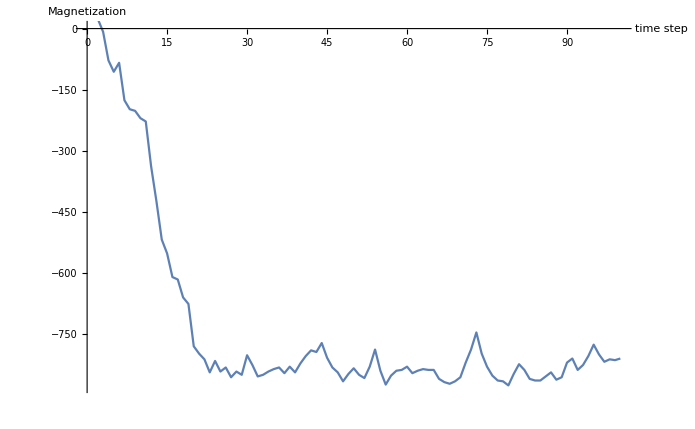

```mathematica
tmax=100; (*Input number of time steps *)
kT=1.7; (*Input temperature *)
n=30;m=30; (*Input Dimensions *)
FullData={};
Magnetization={}
currentArray=RandomInteger[1,{n,m}]/.{0->-1};
 
(*Energy finds the energy of the array based on our equation *)
energy[array_]:=-(Sum[Sum[array⟦i,x⟧array⟦i+1,x⟧,{i,1,n-1}],{x,1,m}]+Sum[Sum[array⟦x,i⟧array⟦x,i+1⟧,{i,1,m-1}],{x,1,n}])

(*Probability takes in a change in energy and a temperature and outputs the probability of a flip *)
Prob[DeltaEnergy_,kT_]:=ⅇ^(-DeltaEnergy/kT) 

(*Flip cell takes in a change in energy and temperature in units of kT and applies our flipping rule *)
Flip[DeltaEnergy_,cell_,kT_]:=If[DeltaEnergy<0,cell/.{1->-1,-1->1},If[Random[]<Prob[DeltaEnergy,kT],cell/.{1->-1,-1->1},cell]] 

(*TestArray takes in a pair of indicies and an array and flips the indicated cell *)
TestArray[i_,j_,array_]:=ReplacePart[array,{i,j}->array⟦i,j⟧/.{1->-1,-1->1}]

(*ToFlipOrNotToFlip takes in an index, an array, and a temperature in units of kT. It creates a test array, flipping the indicated cell. Then the change in energy produced by this flip is calculated. Then the specified index in the array is replaced based on our Flip function (this means sometimes it is simply replaced by itself, and othertimes it is actually flipped) *)
ToFlipOrNotToFlip[i_,j_,array_,kT_]:=Block[{deltaEnergy,testarray},
testarray=TestArray[i,j,array];deltaEnergy=energy[testarray]-energy[array];
ReplacePart[array,{i,j}->Flip[deltaEnergy,array⟦i,j⟧,kT]]]

(*Now we put it all together into the loops. The outer most loop runs our program for a certain number of time steps *)
For[t=1,t⩽tmax,t++,

(*The middle loop goes through each column *)
For[j=1,j≤m,j++,

(*The inner most goes through each cell in a given column, applying our ToFlipOrNotToFlip to each cell sequentially. The new array is stored at each step*)
For[i=1,i≤n,i++,currentArray=ToFlipOrNotToFlip[i,j,currentArray,kT];]];

(*Outside of our inner two loops, we add the current array to our list of full data and the sum of all of the spins to our list of the magnetiziations*)
FullData=Append[FullData,currentArray];
Magnetization=Append[Magnetization,Total[Total[currentArray]]];
]


(*Outside of all of the loops, we plot our data*)
Animate[ArrayPlot[FullData⟦k⟧,ColorRules->{1->Red,-1->Blue}],{k,1,tmax,1}]

ListPlot[Magnetization,Joined->True,AxesLabel->{"time step","Magnetization"}]
```

Excellent, that looks much better!

## Full code, Take 3, wherein I realize that a) we need periodic boundary conditions and b) that is WAY easier to code.

### Let’s define the change in energy in terms of the neighbors.

We can define the change in energy in terms of the neighbors. Now this is a pain in Mathematica because because it counts the first index of an array as 1 and not 0. So if I want to use periodic boundary conditions and have first index-1=nth index, I can’t do Mod[i-1,n], which returns 0 when i=1. Instead, I need to do Mod[i-2,n]+1, which returns n-1+1=n. This will be easier in python. The function for the change in energy is the only function I’ll store separately.

```mathematica
deltaEnergy[i_,j_,array_]:=
(array⟦i,j⟧array⟦i,Mod[j,m]+1⟧+array⟦i,j⟧array⟦i,Mod[j-2,m]+1⟧ (*neighbors in same row *)+
array⟦i,j⟧array⟦Mod[i-2,n]+1,j⟧+ (*neighbor in row above*)
array⟦i,j⟧array⟦Mod[i,n]+1,j⟧) (*neighbor in row below*)-((array⟦i,j⟧/.{-1->1,1->-1})array⟦i,Mod[j,m]+1⟧+(array⟦i,j⟧/.{-1->1,1->-1})array⟦i,Mod[j-2,m]+1⟧+(*neighbors in same row *)
(array⟦i,j⟧/.{-1->1,1->-1})array⟦Mod[i-2,n]+1,j⟧+(*neighbor in row above*)
(array⟦i,j⟧/.{-1->1,1->-1})array⟦Mod[i,n]+1,j⟧) (*neighbor in row below *)
```

As a side note, our test for whether or not we flip is sort of redundant. I don’t need all of my terms that were in the previous if statement, because if the change in energy is less than 0, then I have e^(- negative number)=e^(positive number), which is always greater than 1. So it will be included in the inner part of that earlier if statement.

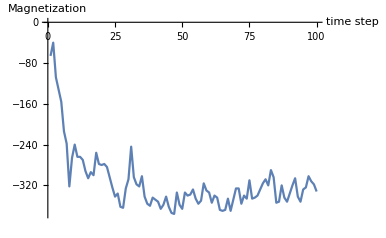

```mathematica
tmax=100; (*Input number of time steps *)
kT=2.2; (*Input temperature *)
n=20;m=20; (*Input Dimensions *)
fullData={};
magnetization={};
currentArray=RandomInteger[1,{n,m}]/.{0->-1};
fullData=Append[fullData,currentArray];
For[t=1,t⩽tmax,t++,

For[j=1,j≤m,j++,

For[i=1,i≤n,i++,
(*Print[{i,j}];*)
(*Print[currentArray//MatrixForm];*)
If[RandomReal[]<ⅇ^(-deltaEnergy[i,j,currentArray]/kT),(*Print["flip"]; *)currentArray⟦i,j⟧=-currentArray⟦i,j⟧,currentArray⟦i,j⟧=currentArray⟦i,j⟧];
(*Print[currentArray//MatrixForm]*);
]];

(*Outside of our inner two loops, we add the current array to our list of full data and the sum of all of the spins to our list of the magnetiziations*)
fullData=Append[fullData,currentArray];
magnetization=Append[magnetization,Total[Total[currentArray]]];
]
Animate[ArrayPlot[fullData⟦k⟧,ColorRules->{1->Red,-1->Blue}],{k,1,tmax,1}]

ListPlot[magnetization,Joined->True,AxesLabel->{"time step","Magnetization"}]
```

## Antiferromagnetic case

Initially, I made the mistake of having the wrong sign on my change in energy--this caused things to anti align instead of align. Let’s do this intentionally now!

```mathematica
deltaEnergyAnti[i_,j_,array_]:=
((array⟦i,j⟧/.{-1->1,1->-1})array⟦i,Mod[j,m]+1⟧+(array⟦i,j⟧/.{-1->1,1->-1})array⟦i,Mod[j-2,m]+1⟧+(*neighbors in same row *)
(array⟦i,j⟧/.{-1->1,1->-1})array⟦Mod[i-2,n]+1,j⟧+(*neighbor in row above*)
(array⟦i,j⟧/.{-1->1,1->-1})array⟦Mod[i,n]+1,j⟧) (*neighbor in row below *)-((array⟦i,j⟧array⟦i,Mod[j,m]+1⟧+array⟦i,j⟧array⟦i,Mod[j-2,m]+1⟧ (*neighbors in same row *)+
array⟦i,j⟧array⟦Mod[i-2,n]+1,j⟧+ (*neighbor in row above*)
array⟦i,j⟧array⟦Mod[i,n]+1,j⟧) (*neighbor in row below*))
```

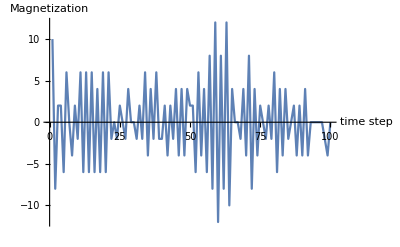

```mathematica
tmax=100; (*Input number of time steps *)
kT=1; (*Input temperature *)
n=20;m=20; (*Input Dimensions *)
fullDataAnti={};
magnetizationAnti={};
currentArray=RandomInteger[1,{n,m}]/.{0->-1};
fullDataAnti=Append[fullDataAnti,currentArray];
For[t=1,t⩽tmax,t++,

For[j=1,j≤m,j++,

For[i=1,i≤n,i++,
(*Print[{i,j}];*)
(*Print[currentArray//MatrixForm];*)
If[RandomReal[]<ⅇ^(-deltaEnergyAnti[i,j,currentArray]/kT),(*Print["flip"]; *)currentArray⟦i,j⟧=-currentArray⟦i,j⟧,currentArray⟦i,j⟧=currentArray⟦i,j⟧];
(*Print[currentArray//MatrixForm]*);
]];

(*Outside of our inner two loops, we add the current array to our list of full data and the sum of all of the spins to our list of the magnetiziations*)
fullDataAnti=Append[fullDataAnti,currentArray];
magnetizationAnti=Append[magnetizationAnti,Total[Total[currentArray]]];
]
Animate[ArrayPlot[fullDataAnti⟦k⟧,ColorRules->{1->Red,-1->Blue}],{k,1,tmax,1}]

ListPlot[magnetizationAnti,Joined->True,AxesLabel->{"time step","Magnetization"}]
```

That’s fun--at a cold temperature, it’s line regions freeze in!